```mathematica
$Assumptions={n∈Integers,0<x0<1}
```

{n∈ℤ,0<x0<1}

```mathematica
f[x_,x0_,δ_]:=Piecewise[{{1/2+Cos[(Pi(x-x0))/(2δ)],Abs[x-x0]<δ},{0,True}}]
```

```mathematica
(∫_(x0-δ)^(x0+δ) (1/2+Cos[(Pi(x-x0))/(2δ)])Sin[Pi n x]ⅆx)/(∫_0^1 (Sin[Pi n x])^2ⅆx)//FullSimplify
```

2 Sin[n π x0] ((4 δ Cos[n π δ])/(π-4 n^2 π δ^2)+Sin[n π δ]/(n π))

#### Fourier Series for f(x) over [0,1]

```mathematica
bk[x_,k_,x0_,δ_]:=∑_(n=1)^k 2 Sin[n π x0] ((4 δ Cos[n π δ])/(π-4 n^2 π δ^2)+Sin[n π δ]/(n π))Sin[π n x];
```

```mathematica
Plot[2 Sin[5π x01] ((4 δ1 Cos[5 π δ1])/(π-4 5^2 π δ1^2)+Sin[5 π δ1]/(5 π))Sin[π 5 x],{x,0,1}]
```

-Graphics-

```mathematica
δ1=1/10;x01=1/10;
```

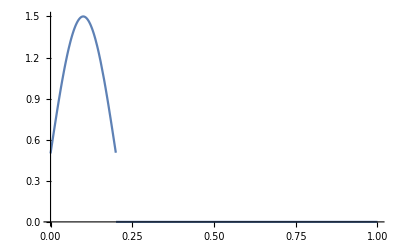

```mathematica
Plot[f[x,x01,δ1],{x,0,1}]
```

```mathematica
b5=Limit[2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π)),n->5]
```

(2+π)/(5 π)

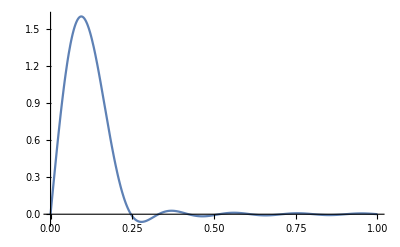

```mathematica
Plot[{bk[x,4,x01,δ1]+b5*Sin[5Pi x]+∑_(n=6)^10 2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π))Sin[π n x]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

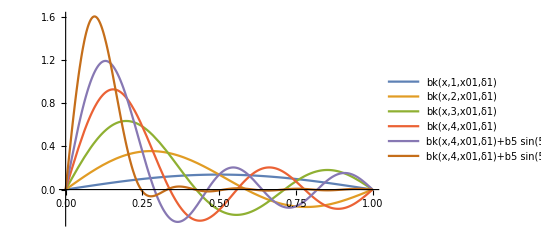

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,4,x01,δ1],bk[x,4,x01,δ1]+b5*Sin[5Pi x],bk[x,4,x01,δ1]+b5*Sin[5Pi x]+∑_(n=6)^10 2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π))Sin[π n x]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/7;
```

```mathematica
b5=Limit[2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π)),n->5]
```

((2+π) Cos[(3 π)/14])/(5 π)

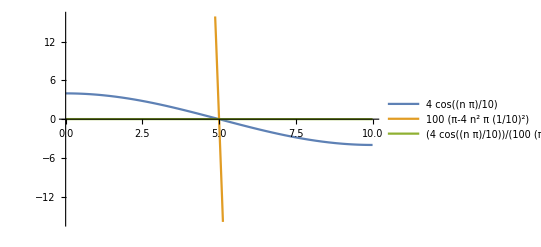

```mathematica
Plot[{4 Cos[(n π)/10],100 (π-4 n^2 π (1/10)^2),(4 Cos[(n π)/10])/(100 (π-4 n^2 π (1/10)^2))}, {n,0,10},PlotLegends->"Expressions"]
```

```mathematica
Limit[(4 Cos[(n π)/10])/(100 (π-4 n^2 π (1/10)^2)),n->5]
```

1/100

```mathematica
Limit[2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π)),n->5]
```

((2+π) Cos[(3 π)/14])/(5 π)

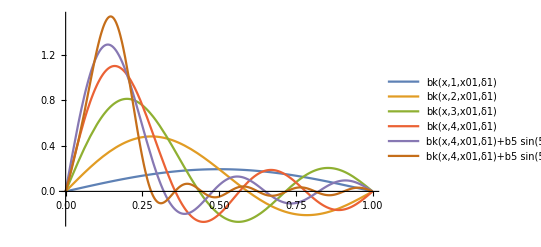

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,4,x01,δ1],bk[x,4,x01,δ1]+b5*Sin[5Pi x],bk[x,4,x01,δ1]+b5*Sin[5Pi x]+∑_(n=6)^10 2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π))Sin[π n x]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/3;
```

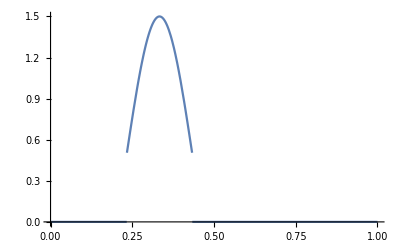

```mathematica
Plot[f[x,x01,δ1],{x,0,1}]
```

```mathematica
b5=Limit[2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π)),n->5]
```

-(√3 (2+π))/(10 π)

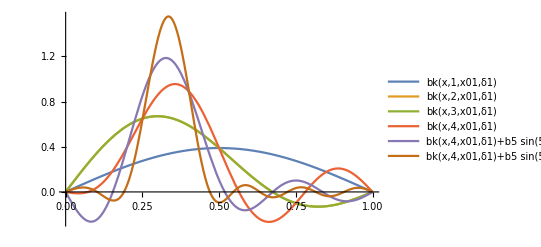

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,4,x01,δ1],bk[x,4,x01,δ1]+b5*Sin[5Pi x],bk[x,4,x01,δ1]+b5*Sin[5Pi x]+∑_(n=6)^10 2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π))Sin[π n x]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/2;
```

```mathematica
b5=Limit[2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π)),n->5]
```

(2+π)/(5 π)

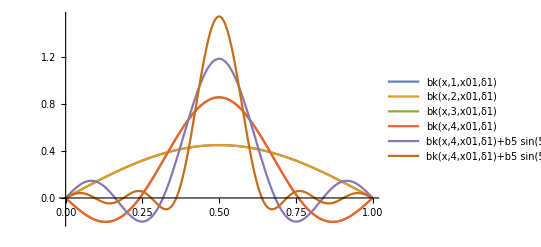

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,4,x01,δ1],bk[x,4,x01,δ1]+b5*Sin[5Pi x],bk[x,4,x01,δ1]+b5*Sin[5Pi x]+∑_(n=6)^10 2 Sin[n π x01] ((4 δ1 Cos[n π δ1])/(π-4 n^2 π δ1^2)+Sin[n π δ1]/(n π))Sin[π n x]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

#### delta = 1/100

```mathematica
δ1=1/100;x01=1/10;
```

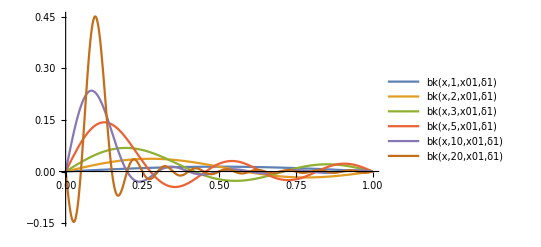

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,5,x01,δ1],bk[x,10,x01,δ1],bk[x,20,x01,δ1]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/7;
```

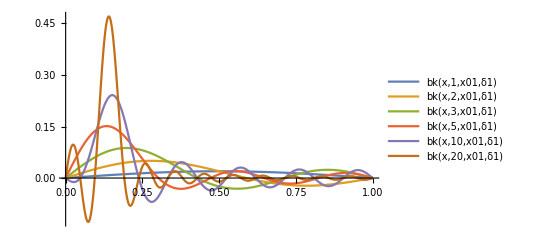

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,5,x01,δ1],bk[x,10,x01,δ1],bk[x,20,x01,δ1]},{x,0,1},PlotLegends->"Expressions", PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/3;
```

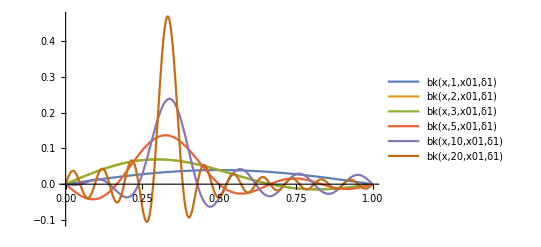

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,5,x01,δ1],bk[x,10,x01,δ1],bk[x,20,x01,δ1]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/2;
```

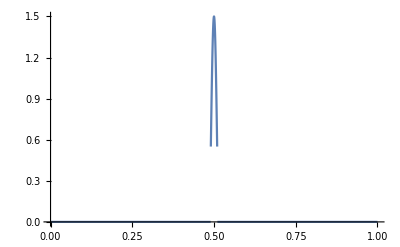

```mathematica
Plot[f[x,x01,δ1],{x,0,1}]
```

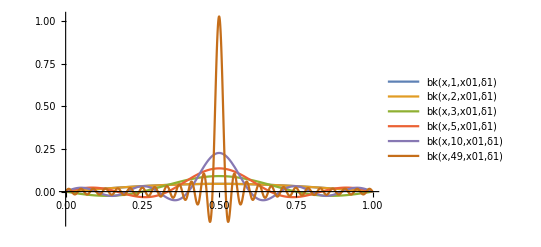

```mathematica
Plot[{bk[x,1,x01,δ1],bk[x,2,x01,δ1],bk[x,3,x01,δ1],bk[x,5,x01,δ1],bk[x,10,x01,δ1],bk[x,49,x01,δ1]},{x,0,1},PlotLegends->"Expressions",PlotRange->Full]
```

## As Initial Velocity

#### Full Solution

```mathematica
u[x_,t_,k_,x0_,δ_]:=∑_(n=1)^k 2 Sin[n π x0] ((4 δ Cos[n π δ])/(π-4 n^2 π δ^2)+Sin[n π δ]/(n π))Sin[π n x]Sin[π n t];
```

```mathematica
δ31=1/100;x03=1/3;
```

```mathematica
Manipulate[Plot[u[x,t,40,x03,δ31],{x,0,1},PlotLegends->"Expressions",PlotRange->{-1,1}],{t,.0001,4}]
```

```mathematica
δ2=1/10;x02=1/10;
```

```mathematica
Manipulate[Plot[u[x,t,4,x02,δ2],{x,0,1},PlotLegends->"Expressions",PlotRange->{-1,1}],{t,.0001,4}]
```

### Energy

```mathematica
e1[n_,x0_,δ_]:=(2 Sin[n π x0] ((4 δ Cos[n π δ])/(π-4 n^2 π δ^2)+Sin[n π δ]/(n π)))^2
```

#### delta = 1/100

```mathematica
δ1=1/100;x01=1/10;
```

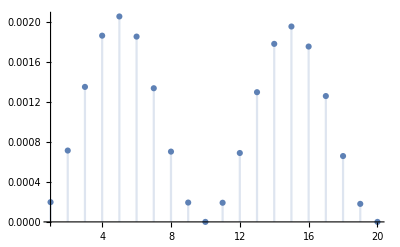

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,20},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/7;
```

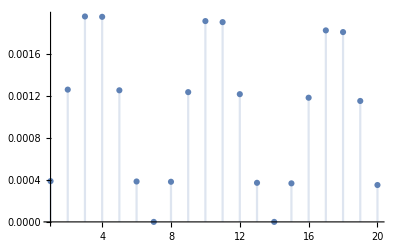

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,20},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/3;
```

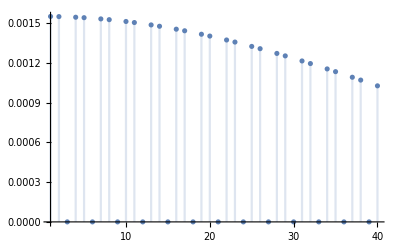

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,40},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/2;
```

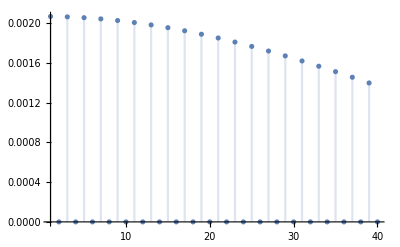

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,40},PlotLegends->"Expressions",PlotRange->Full]
```

#### delta = 1/10

```mathematica
δ1=1/10;x01=1/10;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

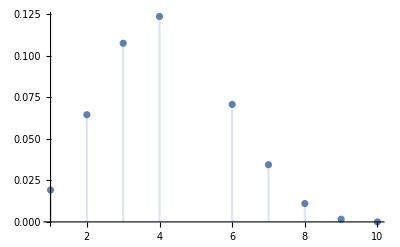

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,10},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/7;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

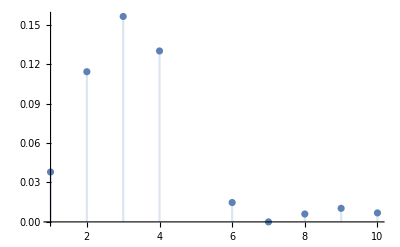

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,10},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/3;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

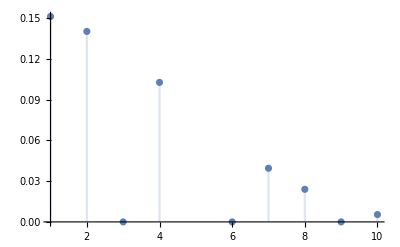

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,10},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/2;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

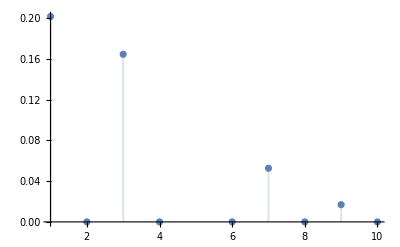

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,1,10},PlotLegends->"Expressions",PlotRange->Full]
```

## As Initial Displacement

#### Full Solution

```mathematica
ud[x_,t_,k_,x0_,δ_]:=∑_(n=1)^k 2 Sin[n π x0] ((4 δ Cos[n π δ])/(π-4 n^2 π δ^2)+Sin[n π δ]/(n π))Sin[π n x]Cos[π n t];
```

```mathematica
δ31=1/100;x03=1/2;
```

```mathematica
Manipulate[Plot[ud[x,t,40,x03,δ31],{x,0,1},PlotLegends->"Expressions",PlotRange->{-1,1}],{t,.0001,4}]
```

```mathematica
δ2=1/10;x02=1/2;
```

```mathematica
Manipulate[Plot[ud[x,t,4,x02,δ2],{x,0,1},PlotLegends->"Expressions",PlotRange->{-1,1}],{t,.0001,4}]
```

### Energy

```mathematica
e1[k_,x0_,δ_]:=(2 Sin[n π x0] ((4 δ Cos[n π δ])/(π-4 n^2 π δ^2)+Sin[n π δ]/(n π)))^2
```

#### delta = 1/100

```mathematica
δ1=1/100;x01=1/10;
```

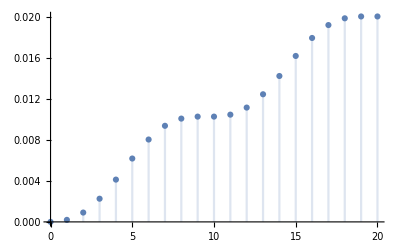

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,20},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/7;
```

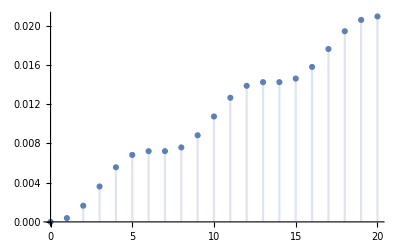

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,20},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/3;
```

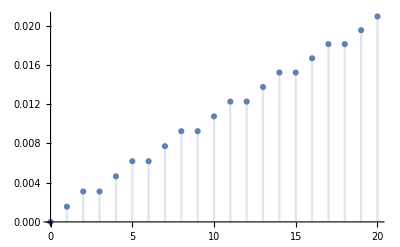

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,20},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/100;x01=1/2;
```

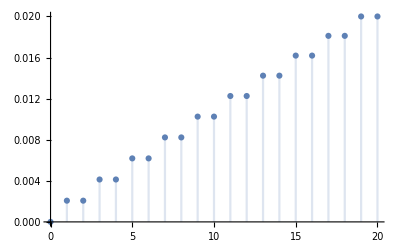

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,20},PlotLegends->"Expressions",PlotRange->Full]
```

#### delta = 1/10

```mathematica
δ1=1/10;x01=1/10;
```

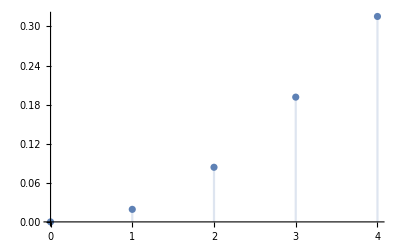

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,4},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/7;
```

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,4},PlotLegends->"Expressions",PlotRange->Full]
```

-Graphics-

```mathematica
δ1=1/10;x01=1/3;
```

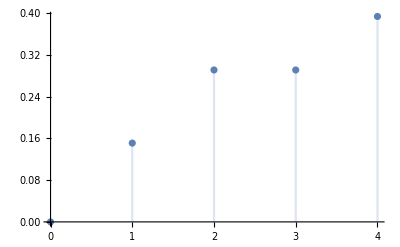

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,4},PlotLegends->"Expressions",PlotRange->Full]
```

```mathematica
δ1=1/10;x01=1/2;
```

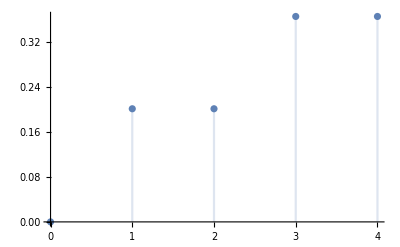

```mathematica
DiscretePlot[e1[n,x01,δ1],{n,0,4},PlotLegends->"Expressions",PlotRange->Full]
```

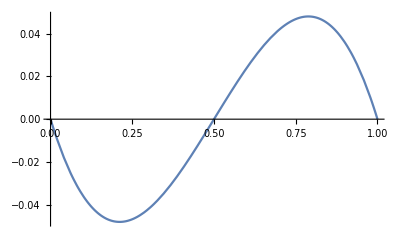

```mathematica
Plot[x(1-x) (x-1/2),{x,0,1}]
```

```mathematica
fun[x_]:=x Exp[-x]
```

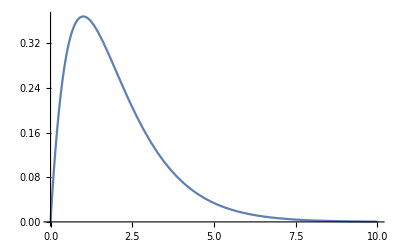

```mathematica
Plot[fun[x],{x,0,10}]
```